## Generate data with errors, OLS vs MLE

```mathematica
IntegerPart@AbsoluteTime[]
```

3906607785

```mathematica
SeedRandom[IntegerPart@AbsoluteTime[]];
```

```mathematica
error=.5;
dat=Table[{x,5.x-3.+2. RandomVariate[NormalDistribution[0,error]]},{x,0,3,.1}];
```

```mathematica
Length@dat
```

31

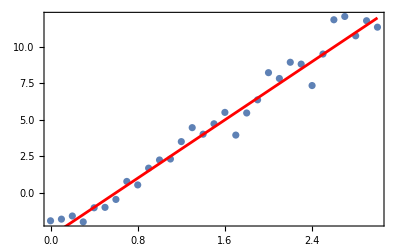

```mathematica
Show[ListPlot[dat,Axes->False],Plot[5.x-3.,{x,0,3},PlotStyle->Red,Axes->False],Frame->True]
```

```mathematica
Dimensions@dat
```

{31,2}

## OLS (Ordinary Least Squares)

```mathematica
Clear[modelo]
```

```mathematica
modelo[x_]=a x + b;
```

```mathematica
mincuad=Sum[(dat[[k,2]]-modelo[dat[[k,1]]])^2,{k,Length@dat}]
```

(-1.92615-b)^2+(11.3644-3. a-b)^2+(11.8072-2.9 a-b)^2+(10.7706-2.8 a-b)^2+(12.0996-2.7 a-b)^2+(11.8725-2.6 a-b)^2+(9.52055-2.5 a-b)^2+(7.35749-2.4 a-b)^2+(8.82878-2.3 a-b)^2+(8.95582-2.2 a-b)^2+(7.84129-2.1 a-b)^2+(8.24187-2. a-b)^2+(6.3767-1.9 a-b)^2+(5.47419-1.8 a-b)^2+(3.9565-1.7 a-b)^2+(5.51462-1.6 a-b)^2+(4.73279-1.5 a-b)^2+(4.01892-1.4 a-b)^2+(4.4679-1.3 a-b)^2+(3.50884-1.2 a-b)^2+(2.31516-1.1 a-b)^2+(2.24833-1. a-b)^2+(1.68797-0.9 a-b)^2+(0.535882-0.8 a-b)^2+(0.775237-0.7 a-b)^2+(-0.459579-0.6 a-b)^2+(-1.00433-0.5 a-b)^2+(-1.03269-0.4 a-b)^2+(-2.00185-0.3 a-b)^2+(-1.59682-0.2 a-b)^2+(-1.81257-0.1 a-b)^2

```mathematica
mincuad//FullSimplify
```

31. (42.6379+3.05 a^2+(-9.31866+b) b+a (-22.0455+3. b))

```mathematica
AbsoluteTiming[solOLS=NMinimize[mincuad,{a,b}]]
```

{0.200183,{18.2819,{a→5.04218,b→-2.90394}}}

```mathematica
AbsoluteTiming[solOLS=FindMinimum[mincuad,{a,b},Method->"LevenbergMarquardt"]]
```

{0.003646,{18.2819,{a→5.04218,b→-2.90394}}}

```mathematica
otraSol=Fit[dat, {1,x},x]
```

-2.90394+5.04218 x

```mathematica
eca=D[mincuad,a];
ecb=D[mincuad,b];
```

```mathematica
Solve[{eca==0,ecb==0},{a,b}]
```

{{a→5.04218,b→-2.90394}}

## MLE (Maximum Likelihood Estimator)

```mathematica
Clear[modelo,dist]
```

```mathematica
modelo[x_]=a x + b;
```

```mathematica
dist[y_,x_]=PDF[NormalDistribution[modelo[x],σ],y]
```

(ⅇ^(-(-b-a x+y)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
Log[Product[dist[dat[[k,2]],dat[[k,1]]],{k,Length@dat}]]//PowerExpand//FullSimplify
```

1/σ^2(-660.888-47.275 a^2+a (341.705-46.5 b)+(144.439-15.5 b) b-28.4871 σ^2-31. σ^2 Log[σ])

```mathematica
lmle1=PowerExpand[Log[Product[dist[dat[[k,2]],dat[[k,1]]],{k,Length@dat}]]]//FullSimplify
```

1/σ^2(-660.888-47.275 a^2+a (341.705-46.5 b)+(144.439-15.5 b) b-28.4871 σ^2-31. σ^2 Log[σ])

```mathematica
AbsoluteTiming[solMLE=NMaximize[{lmle1,σ>0},{a,b,σ}]]
```

{4.06441,{-35.8019,{a→5.04218,b→-2.90394,σ→0.767945}}}

```mathematica
(a/.solOLS[[2]])-(a/.solMLE[[2]])
```

7.69063×10^-9

```mathematica
Chop[%]
```

7.69063×10^-9

```mathematica
(b/.solOLS[[2]])-(b/.solMLE[[2]])
```

0.

```mathematica
Chop[%]
```

0

Otra forma de la distribución de errores

```mathematica
Clear[a,b,modelo]
```

```mathematica
modelo[x_]=a x + b;
```

```mathematica
dist[y_,x_]=PDF[StudentTDistribution[modelo[x],σ,Length@dat -2],y]
```

(9984397484360291143009697792 √29)/(5014575 π (29+(-b-a x+y)^2/σ^2)^15 σ)

```mathematica
lmle1=PowerExpand[Log[Product[dist[dat[[k,2]],dat[[k,1]]],{k,Length@dat}]]]//FullSimplify;
```

```mathematica
AbsoluteTiming[solMLE=NMaximize[{lmle1,a>0&&σ>0},{a,b,σ}]]
```

{3.61375,{-35.7233,{a→5.04078,b→-2.89809,σ→0.738171}}}

```mathematica
(a/.solOLS[[2]])-(a/.solMLE[[2]])
```

0.00140152

```mathematica
(b/.solOLS[[2]])-(b/.solMLE[[2]])
```

-0.0058517

```mathematica
Chop[%]
```

-0.0058517

## Volviendo a Exoplanetas Maximum Likelihood Estimator

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/michel/cursos/pregrado

```mathematica
exopl=Import["exoplanet.eu_catalog.csv"];
```

```mathematica
masas=Select[exopl[[All,3]],NumberQ];
```

```mathematica
distmasas=SmoothKernelDistribution[Log10@masas];
```

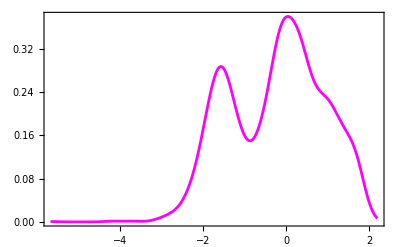

```mathematica
grma=Plot[PDF[distmasas,lm],{lm,-5.68,2.2},Frame->True,Axes->False,PlotStyle->Magenta]
```

```mathematica
modelo=MixtureDistribution[{a1,a2,a3},{NormalDistribution[μ1,σ1],NormalDistribution[μ2,σ2],NormalDistribution[μ3,σ3]}];
```

```mathematica
PDF[modelo,x]
```

(a1 ⅇ^(-(x-μ1)^2/(2 σ1^2)))/((a1+a2+a3) √(2 π) σ1)+(a2 ⅇ^(-(x-μ2)^2/(2 σ2^2)))/((a1+a2+a3) √(2 π) σ2)+(a3 ⅇ^(-(x-μ3)^2/(2 σ3^2)))/((a1+a2+a3) √(2 π) σ3)

```mathematica
loglk=LogLikelihood[modelo,Log10@masas];
```

```mathematica
AbsoluteTiming[sol0=NMaximize[
{loglk,a1>0&&a2>0&&a3>0&&σ1>0&&σ2>0&&σ3>0},{{a1,0.1,1.},{a2,0.1,1.},{a3,0.1,1.},{μ1,-2.,-1.5},{σ1,.2,.7},{μ2,-.5,.5},{σ2,.2,.9},{μ3,1.,2.},{σ3,.2,.9}}]]
```

{40.6294,{-4360.69,{a1→0.912204,a2→1.19695,a3→0.517614,μ1→-1.53623,σ1→0.534258,μ2→0.0969365,σ2→0.428354,μ3→1.24605,σ3→0.348639}}}

```mathematica
AbsoluteTiming[sol1=NMaximize[
{loglk,a1>0&&a2>0&&a3>0&&σ1>0&&σ2>0&&σ3>0},{{a1,0.1,1.},{a2,0.1,1.},{a3,0.1,1.},{μ1,-2.,-1.5},{σ1,.2,.7},{μ2,-.5,.5},{σ2,.2,.9},{μ3,1.,2.},{σ3,.2,.9}},Method->"DifferentialEvolution"]]
```

{86.0716,{-4360.69,{a1→5.25559,a2→6.89567,a3→2.98242,μ1→-1.53622,σ1→0.534264,μ2→0.0969174,σ2→0.428331,μ3→1.24601,σ3→0.348658}}}

```mathematica
AbsoluteTiming[sol2=NMaximize[
{loglk,a1>0&&a2>0&&a3>0&&σ1>0&&σ2>0&&σ3>0},{{a1,0.1,1.},{a2,0.1,1.},{a3,0.1,1.},{μ1,-2.,-1.5},{σ1,.2,.7},{μ2,-.5,.5},{σ2,.2,.9},{μ3,1.,2.},{σ3,.2,.9}},Method->"SimulatedAnnealing"]]
```

{11.7659,{-4360.69,{a1→0.985437,a2→1.29305,a3→0.559169,μ1→-1.53623,σ1→0.534258,μ2→0.0969366,σ2→0.428354,μ3→1.24605,σ3→0.348639}}}

```mathematica
AbsoluteTiming[sol3=NMaximize[
{loglk,a1>0&&a2>0&&a3>0&&σ1>0&&σ2>0&&σ3>0},{{a1,0.1,1.},{a2,0.1,1.},{a3,0.1,1.},{μ1,-2.,-1.5},{σ1,.2,.7},{μ2,-.5,.5},{σ2,.2,.9},{μ3,1.,2.},{σ3,.2,.9}},Method->"NelderMead"]]
```

{15.9078,{-4360.69,{a1→0.997295,a2→1.30861,a3→0.565897,μ1→-1.53623,σ1→0.534258,μ2→0.0969366,σ2→0.428354,μ3→1.24605,σ3→0.348639}}}

```mathematica
AbsoluteTiming[sol4=NMaximize[
{loglk,a1>0&&a2>0&&a3>0&&σ1>0&&σ2>0&&σ3>0},{{a1,0.1,1.},{a2,0.1,1.},{a3,0.1,1.},{μ1,-2.,-1.5},{σ1,.2,.7},{μ2,-.5,.5},{σ2,.2,.9},{μ3,1.,2.},{σ3,.2,.9}},Method->"RandomSearch"]]
```

{426.439,{-4360.69,{a1→0.923166,a2→1.21134,a3→0.523834,μ1→-1.53623,σ1→0.534258,μ2→0.0969365,σ2→0.428354,μ3→1.24605,σ3→0.348639}}}

```mathematica
AbsoluteTiming[sol5=NMaximize[
{loglk,a1>0&&a2>0&&a3>0&&σ1>0&&σ2>0&&σ3>0},{{a1,0.1,1.},{a2,0.1,1.},{a3,0.1,1.},{μ1,-2.,-1.5},{σ1,.2,.7},{μ2,-.5,.5},{σ2,.2,.9},{μ3,1.,2.},{σ3,.2,.9}},Method->"Couenne"]]
```

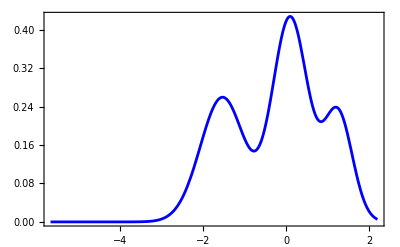

```mathematica
grMLE=Show[Plot[PDF[modelo/.sol0[[2]],lgm],{lgm,-5.68,2.2},PlotStyle->Blue,Frame->True,Axes->False],PlotRange->All]
```

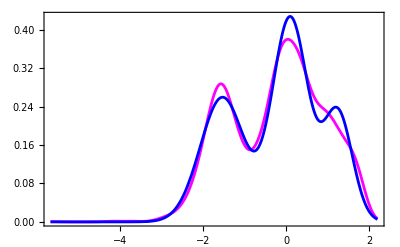

```mathematica
Show[grma,grMLE,PlotRange->All]
```

## Base de Datos de Exoplanetas (https : // exoplanetarchive.ipac.caltech.edu)

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/michel/cursos/pregrado

```mathematica
FileNames["*.csv"]
```

{exoplanet.eu_catalog.csv,PS_2023.10.18_04.32.03.csv}

```mathematica
data=Import["PS_2023.10.18_04.32.03.csv"];
```

```mathematica
datos=Drop[data,290];
```

```mathematica
encab=datos[[1]];
```

```mathematica
Table[{k,encab[[k]]},{k,Length@encab}]//TableForm;
```

```mathematica
nmassj=Position[encab,"pl_massj"][[1,1]]
```

54

```mathematica
masasj=Select[datos[[All,nmassj]],NumberQ];
```

```mathematica
Length@masasj
```

3565

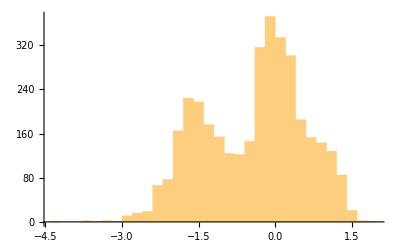

```mathematica
Histogram[Log10@masasj]
```

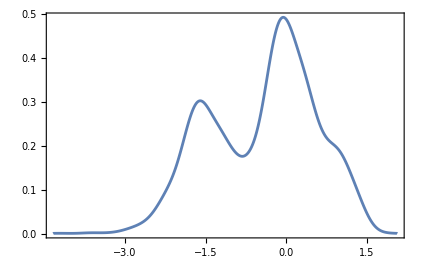

```mathematica
SmoothHistogram[Log10@masasj,Frame->True,Axes->False]
```

```mathematica
Clear[modelo]
```

```mathematica
modelo=MixtureDistribution[{a1,a2,a3},{NormalDistribution[μ1,σ1],NormalDistribution[μ2,σ2],NormalDistribution[μ3,σ3]}];
```

```mathematica
PDF[modelo,x]
```

(a1 ⅇ^(-(x-μ1)^2/(2 σ1^2)))/((a1+a2+a3) √(2 π) σ1)+(a2 ⅇ^(-(x-μ2)^2/(2 σ2^2)))/((a1+a2+a3) √(2 π) σ2)+(a3 ⅇ^(-(x-μ3)^2/(2 σ3^2)))/((a1+a2+a3) √(2 π) σ3)

```mathematica
loglk=LogLikelihood[modelo,Log10@masasj];
```

```mathematica
AbsoluteTiming[sol0=NMaximize[
{loglk,a1>0&&a2>0&&a3>0.1&&σ1>0&&σ2>0&&σ3>0},{{a1,0.1,1.},{a2,0.1,1.},{a3,0.1,1.},{μ1,-2.,-1.5},{σ1,.2,.7},{μ2,-.5,.5},{σ2,.2,.9},{μ3,1.,2.},{σ3,.2,.9}},Method->"SimulatedAnnealing"]]
```

{17.2859,{-4722.13,{a1→0.767695,a2→0.960956,a3→0.35865,μ1→-1.59608,σ1→0.536584,μ2→0.00931894,σ2→0.37704,μ3→0.8873,σ3→0.303106}}}

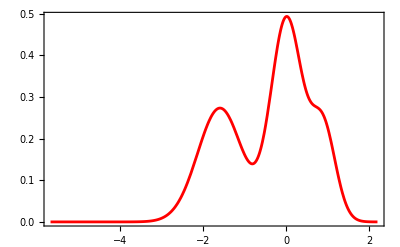

```mathematica
grMLE2=Show[Plot[PDF[modelo/.sol0[[2]],lgm],{lgm,-5.68,2.2},PlotStyle->Red,Frame->True,Axes->False],PlotRange->All]
```

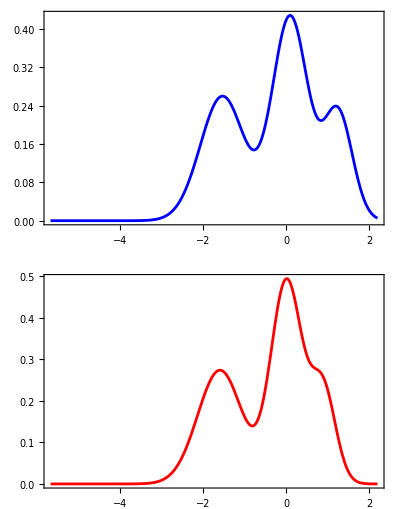

```mathematica
GraphicsGrid[{{grMLE},{grMLE2}}]
```

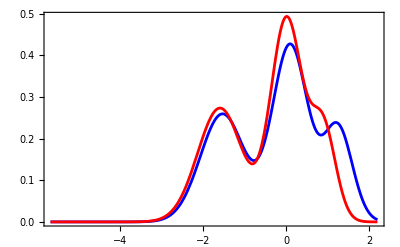

```mathematica
Show[grMLE,grMLE2]
```